```mathematica
CutGraph[g_,vertices_]:=Block[{intersection,sets},
intersection=Subgraph[g,vertices];
sets=Map[SymbolToSets,FindFullFormula[intersection]];intersection
]
```

```mathematica
good=Select[Range[2000],ChromaticPolynomial[ReadGrof[#],4]/48==1&]
```

{46,108,122,216,413,591,593,604,617,627,658,667,754,770,776,783,789,800,814,855,889,904,905,1763,1804,1835,1998,1999}

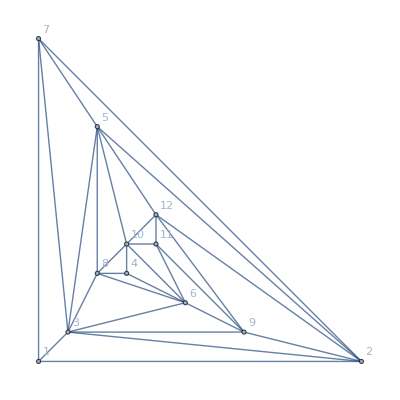

```mathematica
g=Graph[ReadGrof[1999],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]
```

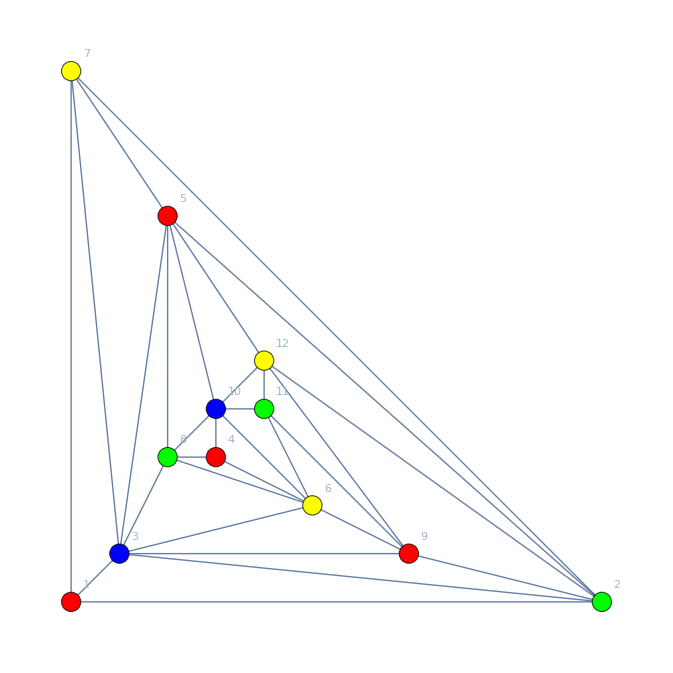
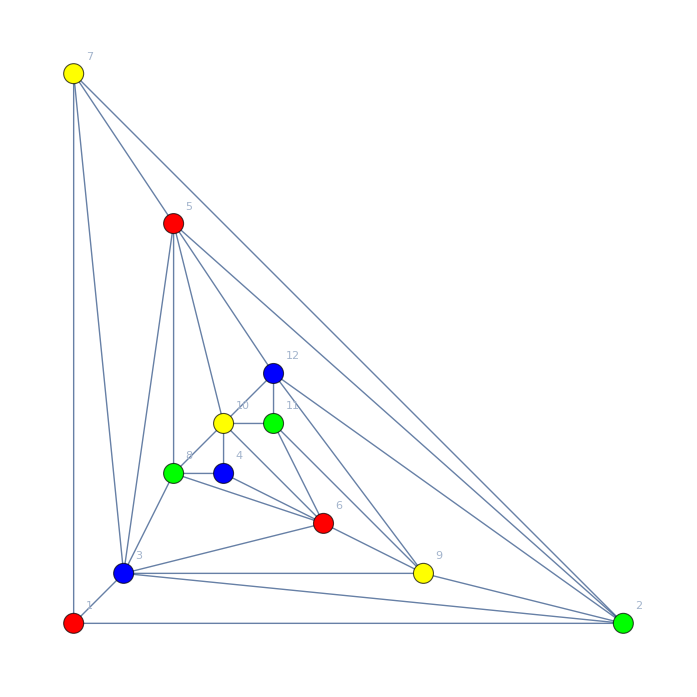

```mathematica
Map[ColorGraph[g,SymbolToSets[ #]]&,FindFullFormula4[g]]
```

```mathematica
FindFullFormula[g]//Length
```

877

```mathematica
Table[Length[FindFullFormula[ReadGrof[k]]],{k,good}]//Tally//Sort
```

{{1,1},{2,1},{5,1},{15,3},{52,7},{203,24},{877,93},{4140,184}}

```mathematica
Table[Length[FindFullFormula[JacobsThalGraph[k]]],{k,9}]//Tally//Sort
```

{{2,1},{8,1},{22,1},{82,1},{324,1},{1430,1},{6850,1},{35444,1},{196506,1}}

```mathematica
Map[First,%]/2
```

{1,4,11,41,162,715,3425,17722,98253}

```mathematica
Map[First,Table[Length[FindFullFormula4[JacobsThalGraph[k]]],{k,9}]//Tally//Sort]
```

{1,3,5,11,21,43,85,171,341}

```mathematica
Map[Last,%]
```

{1,1,1,3,7,24,93,184}

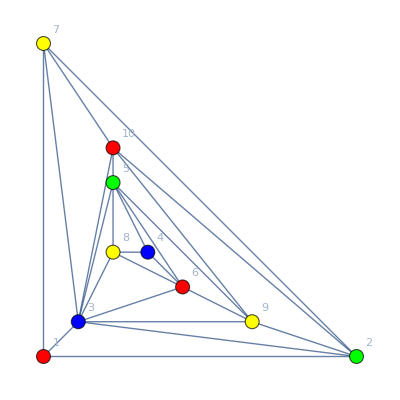

```mathematica
ColorGraph[g,SymbolToSets[ FindFullFormula4[g]//First]]
```

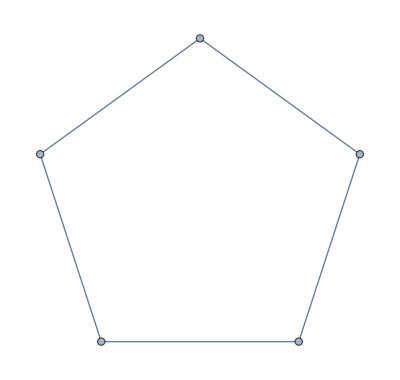

```mathematica
CutGraph[g,{1,7,4,6,2}]
```